## Ejemplos de Tablas

```mathematica
f[T_]:= (t^2) - 100 t
```

```mathematica
fTable = ParallelTable[f[t],{t,0,120}]
```

{0,-99,-196,-291,-384,-475,-564,-651,-736,-819,-900,-979,-1056,-1131,-1204,-1275,-1344,-1411,-1476,-1539,-1600,-1659,-1716,-1771,-1824,-1875,-1924,-1971,-2016,-2059,-2100,-2139,-2176,-2211,-2244,-2275,-2304,-2331,-2356,-2379,-2400,-2419,-2436,-2451,-2464,-2475,-2484,-2491,-2496,-2499,-2500,-2499,-2496,-2491,-2484,-2475,-2464,-2451,-2436,-2419,-2400,-2379,-2356,-2331,-2304,-2275,-2244,-2211,-2176,-2139,-2100,-2059,-2016,-1971,-1924,-1875,-1824,-1771,-1716,-1659,-1600,-1539,-1476,-1411,-1344,-1275,-1204,-1131,-1056,-979,-900,-819,-736,-651,-564,-475,-384,-291,-196,-99,0,101,204,309,416,525,636,749,864,981,1100,1221,1344,1469,1596,1725,1856,1989,2124,2261,2400}

```mathematica
fInterpol = Interpolation[fTable]
```

InterpolatingFunction[…]

```mathematica
Evaluate[fInterpol[40]]
```

-2379

InterpolatingFunction::dmval: Input value {0.00245143} lies outside the range of data in the interpolating function. Extrapolation will be used.

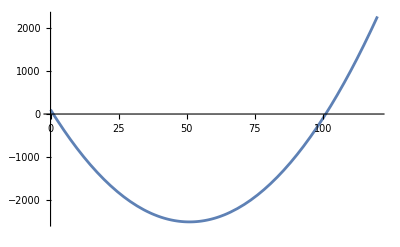

```mathematica
Plot[Evaluate[fInterpol[t]],{t,0,120}]
```

```mathematica
xsol = NDSolve[{x''[t]==x[t]^2,x[0]==1,x'[0]==0},x,{t,0,2},AccuracyGoal->20, PrecisionGoal->20, WorkingPrecision->100 ]
```

{{x→InterpolatingFunction[…]}}

```mathematica
Length[(x/. xsol[[1]])@ValuesOnGrid]
```

503

```mathematica
Evaluate[x[2]/.xsol[[1]]]
```

6.32198680721046227225847809065681241521485530943139043021264638929889100784283181686001926585831514

```mathematica
NIntegrate[Evaluate[x[t] /. xsol], {t,0,2}]
```

{4.32708608667379824797137836834424579180580338362200156178402979452838198077850554408991797250054}

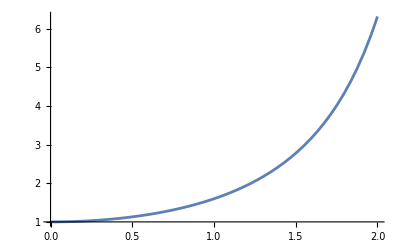

```mathematica
Plot[Evaluate[x[t] /. xsol],{t,0,2} ]
```

```mathematica
sol=NDSolve[{x''[t]==y[t] x[t],y'[t]==-(1/(x[t]^2+y[t]^2)),x[0]==1,x'[0]==0,y[0]==0},{x,y},{t,0,100},AccuracyGoal->20, PrecisionGoal->20 , WorkingPrecision->100]
```

{{x→InterpolatingFunction[{{0, 100.0000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000}}, <>],y→InterpolatingFunction[{{0, 100.0000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000}}, <>]}}

```mathematica
Length[(x/. sol[[1]])@ValuesOnGrid]
```

8539

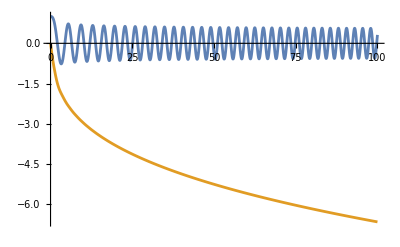

```mathematica
Plot[Evaluate[{x[t], y[t]} /. sol], {t, 0, 100}, PlotRange -> All, PlotPoints -> 200]
```

## Sistema LZ

```mathematica
β = 0.3; Ω = 0.2;
```

```mathematica
alphas=NDSolve[{x'[t]-  2y'[t] x[t] + I Ω(1 + x[t]^2)== 0 ,y'[t] == I(Ω x[t] - (β^2 )t),z'[t]Exp[-2 y[t]]+ I Ω == 0, x[-100]==y[-100]==z[-100]== 0},{x,y, z},{t,-110, 110}, PrecisionGoal->15]
```

{{x→InterpolatingFunction[…],y→InterpolatingFunction[…],z→InterpolatingFunction[…]}}

```mathematica
Length[(x/. xsol[[1]])@ValuesOnGrid]
```

503

```mathematica
Evaluate[{x[10], y[10],z[10]} /. alphas]
```

{{-0.6417+1.87667 ⅈ,0.798042+445.842 ⅈ,1.50046+1.29703 ⅈ}}

```mathematica
Evaluate[{z[10]} /. alphas]
```

{{1.50046+1.29703 ⅈ}}

```mathematica
Exp[-π(Ω^2/β^2)]
```

0.24752

```mathematica
Plot[{Evaluate[(Abs[x[t]]^2 )Exp[-2Re[y[t]]]/. alphas], Evaluate[Abs[Exp[- y[t]] ]^2 /. alphas],Exp[-π(Ω^2/β^2)], 1- Exp[-π(Ω^2/β^2)]}, {t, -30, 60}, 
PlotLabel->Style["Probabilidades de transición  β = 0.3 , Ω = 0.2, ψ (0) = |g⟩ ", 16, FontFamily->"Times New Roman", Black],
PlotLegends-> {"P_(g -> e)(t)", "P_(g -> g)(t)", "exp(-π Ω^2 / β^2)","1-exp(-π Ω^2 / β^2)"},PlotLabels->{"","",Style["0.675", 14,FontFamily->"Times New Roman",GrayLevel[0.26]]},
AxesLabel-> {Style["t",16,FontFamily->"Times New Roman",GrayLevel[0.26]] , Style["P_g(t)",16,FontFamily->"Times New Roman",GrayLevel[0.26]]},
FrameTicksStyle->{{20,2},{20,20}},AspectRatio->1, ImageSize->500]
```

-Graphics-

```mathematica
Plot[{Evaluate[(Abs[z[t]]^2) Exp[-2Re[y[t]]]/. alphas], Evaluate[Abs[Exp[y[t]] + Exp[-y[t]] x[t] z[t]]^2 /. alphas], Exp[-π(Ω^2/β^2)], 1- Exp[-π(Ω^2/β^2)]}, {t, -30, 60},
 PlotLabel->Style["Probabilidades de transición β = 0.3, Ω = 0.2, ψ (0) = |e⟩ ", 16, FontFamily->"Times New Roman", Black],
PlotLegends-> {"P_(e -> g)(t)", "P_(e -> e)(t)", "exp(-π Ω^2 / β^2)","1-exp(-π Ω^2 / β^2)"}, PlotLabels->{"","",Style["0.675", 14,FontFamily->"Times New Roman",GrayLevel[0.26]]},AxesLabel-> {Style["t",16,FontFamily->"Times New Roman",GrayLevel[0.26]] , Style["P_e(t)",16,FontFamily->"Times New Roman",GrayLevel[0.26]]},
FrameTicksStyle->{{20,2},{20,20}},AspectRatio->1, ImageSize->500]
```

-Graphics-

```mathematica
NIntegrate[Evaluate[-Exp[(0.1-I 10)t]Exp[-2 y[t]]z[t]^2 /. alphas], {t, 0, 10}]
```

{0.186635+0.20673 ⅈ}

```mathematica
I1[Γ_, ω_, T_]:= NIntegrate[Evaluate[-Exp[(Γ-I ω)t]Exp[-2 y[t]]z[t]^2 /. alphas], {t, 0, T}]
```

```mathematica
I2[Γ_, ω_, T_]:= NIntegrate[Evaluate[-Exp[(Γ+I ω)t]Exp[-2y[t]]x[t]^2 /. alphas], {t,0,T}]
```

```mathematica
I3[Γ_, ω_, T_]:= NIntegrate[Evaluate[-Exp[(Γ-I ω)t]Exp[-2y[t]]z[t] /. alphas],{t,0,T}]
```

```mathematica
I4[Γ_,ω_,T_]:= NIntegrate[Evaluate[Exp[(Γ+I ω)t](x[t]+Exp[-2y[t]](x[t]^2)z[t]) /. alphas], {t,0,T}]
```

```mathematica
S1[Γ_,ω_,T_]:=2Γ Exp[-2Γ T](I1[Γ, ω,T]I2[Γ, ω,T]+I3[Γ, ω,T]I4[Γ, ω,T])
```

```mathematica
S1[0.1,10,40]
```

{0.0195328+0.000167427 ⅈ}

```mathematica
G1=ListLinePlot[ParallelTable[{ω,25+Re[S1[0.1,ω,40]]},{ω,-10,10,0.2}],PlotRange->{-0.5,32.5},Filling->25,Joined->True,AxesOrigin->None,
Frame->True,Axes->False,PlotStyle->Directive[Black,Thickness[0.002]],PlotLegends->"t=40",
FrameLabel->{Style["ω",30,FontFamily->"Times New Roman",Black],
Style["Re[S(ω,Γ,t)]",25,FontFamily->"Times New Roman",Black],Style["Γ=0.1,β=0.3,t=40",20]},
FrameTicksStyle->{{20,2},{20,20}},PlotRangePadding->0,AspectRatio->1,
ImageSize->500,FillingStyle->Directive[RGBColor[0.,0.85,0],Opacity[.2]]]
```

## Resolución del sistema por pasos

Valores de parametros usados como ejemplo.

```mathematica
β = 0.707; Ω = 0.25; h = 1;
```

Ecuación diferencial para α_+

```mathematica
alphaMas= NDSolveValue[{y'[t]- I Ω  y[t]^2 + 2 I  (β^2)t y[t] + I  Ω==0,y[0]==0}, y, {t,-40,40}]
```

InterpolatingFunction[…]

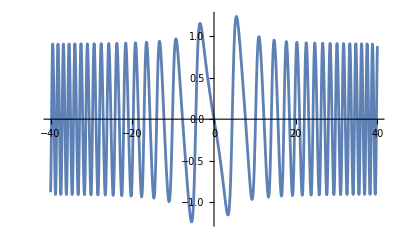

```mathematica
Plot[Im[alphaMas[t]], {t, -40, 40}]
```

```mathematica
alphaMas[12]
```

0.57469+0.25698 ⅈ

Ecuación diferencial para α_z

```mathematica
alphaZ[T_] := I(Ω NIntegrate[alphaMas[t], {t, 0 , T}] - (β^ 2)( T^2)( 0.5))
```

```mathematica
alphaZ[30]
```

0.335219-30.2466 ⅈ

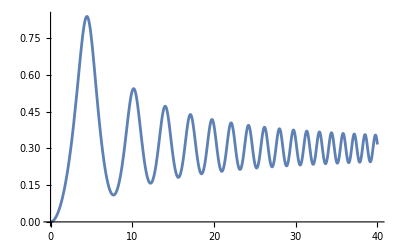

```mathematica
Plot[Re[alphaZ[t]], {t, 0, 40}]
```

A partir de la expresión para α_z creamos una tabla de valores y los interpolamos para obtener una “función numerica integrable” de α_z

```mathematica
alphaZInter = Interpolation[Table[alphaZ[t],{t,0,30}]]
```

InterpolatingFunction[…]

```mathematica
NIntegrate[alphaZInter[t], {t, 1, 10}]
```

3.02247-13.2524 ⅈ

Ecuación diferencial para α_-

```mathematica
alphaMenos[T_] := -I Ω NIntegrate[Exp[2 alphaZInter[t]], {t, 1, T}]
```

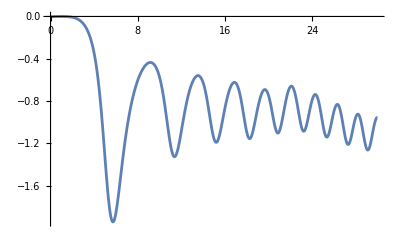

```mathematica
Plot[Re[alphaMenos[t]], {t, 0, 30}]
```